```mathematica
ArcLength[{x,x^2},{x,a,b}]
```

1/4 (-2 a √(1+4 a^2)+2 b √(1+4 b^2)-ArcSinh[2 a]+ArcSinh[2 b])

```mathematica
Plot3D[1/4 (-2 a √(1+4 a^2)+2 b √(1+4 b^2)-ArcSinh[2 a]+ArcSinh[2 b]),{a,-8,8},{b,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[1/4 (-2 a √(1+4 a^2)+2 b √(1+4 b^2)-ArcSinh[2 a]+ArcSinh[2 b]),{a,b}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
FullSimplify[{Abs[-2 a √(1+4 a^2)],Abs[2 b √(1+4 b^2)],Abs[ArcSinh[2 a]],Abs[ArcSinh[2 b]]}/(Total@{Abs[-2 a √(1+4 a^2)],Abs[2 b √(1+4 b^2)],Abs[ArcSinh[2 a]],Abs[ArcSinh[2 b]]}),{a,b}∈Reals]
```

{(2 √(1+4 a^2) Abs[a])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),(2 √(1+4 b^2) Abs[b])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 a]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 b]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]])}

```mathematica
Plot3D[
{(2 √(1+4 a^2) Abs[a])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),(2 √(1+4 b^2) Abs[b])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 a]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 b]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]])}
,{a,b}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
Plot3D[
{(2 √(1+4 a^2) Abs[a])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),(2 √(1+4 b^2) Abs[b])/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 a]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]]),Abs[ArcSinh[2 b]]/(2 √(1+4 a^2) Abs[a]+2 √(1+4 b^2) Abs[b]+Abs[ArcSinh[2 a]]+Abs[ArcSinh[2 b]])}
,{a,b}∈Disk[]]
```

-Graphics3D-

```mathematica
FullSimplify[{x,x^3}/(Total@{x,x^3}),x∈Reals]
```

{1/(1+x^2),x^2/(1+x^2)}

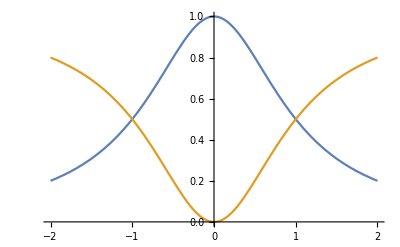

```mathematica
Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-2,2}]
```

```mathematica
FullSimplify[{α x,β x^3}/(Total@{x,x^3}),{x,α,β}∈Reals]
```

{α/(1+x^2),(x^2 β)/(1+x^2)}

```mathematica
Manipulate[
Plot[{α/(1+x^2),(x^2 β)/(1+x^2)},{x,-2,2},PlotRange->{-1,1}]
,{α,-1,1},{{β,1},-1,1}
]
```

```mathematica
FullSimplify[{Abs[α x],Abs[β x^3]}/(Total@{Abs[α x],Abs[β x^3]}),{x,α,β}∈Reals]
```

{Abs[α]/(Abs[α]+x^2 Abs[β]),(x^2 Abs[β])/(Abs[α]+x^2 Abs[β])}

```mathematica
Manipulate[
Plot[{Abs[α]/(Abs[α]+x^2 Abs[β]),(x^2 Abs[β])/(Abs[α]+x^2 Abs[β])},{x,-2,2},PlotRange->{-1,1}]
,{α,-1,1},{{β,1},-1,1}
]
```

```mathematica
With[{list={Abs[α x],Abs[β x^2],Abs[γ x^3]}},
FullSimplify[list/(Total@list),{x,α,β,γ}∈Reals]
]
```

{Abs[x α]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),(x^2 Abs[β])/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),Abs[x^3 γ]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ])}

```mathematica
Manipulate[
Plot[
{Abs[x α]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),(x^2 Abs[β])/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),Abs[x^3 γ]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ])}
,{x,-2,2},PlotRange->{-1,1}]
,{α,-1,1},{{β,1},-1,1},{{γ,0},-1,1}
]
```

```mathematica
Integrate[Abs[x α]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),{x,0,∞}]
```

$Aborted

```mathematica
Integrate[Abs[x α]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ]),{x,0,∞}]/.{α->1,β->1,γ->1}
```

$Aborted

```mathematica
Abs[x α]/(Abs[x α]+x^2 Abs[β]+Abs[x^3 γ])/.{α->1,β->1,γ->1}
```

Abs[x]/(x^2+Abs[x]+Abs[x]^3)

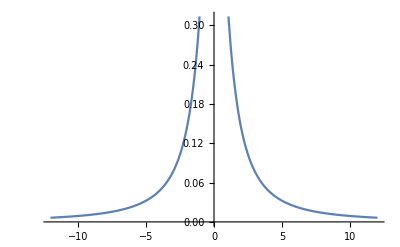

```mathematica
Plot[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,-12.,12.}]
```

```mathematica
Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,-100,100}]
```

-(2 (π-6 ArcTan[67 √3]))/(3 √3)

```mathematica
Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),x]
```

∫Abs[x]/(x^2+Abs[x]+Abs[x]^3)ⅆx

```mathematica
Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,-a,a}]
```

ConditionalExpression[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),Re[a]>0&&Im[a]==0]

```mathematica
FullSimplify[Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,-a,a}],a∈Reals]
```

ConditionalExpression[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),a>0]

```mathematica
FullSimplify[Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,-a,a}],a∈]
```

-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3)

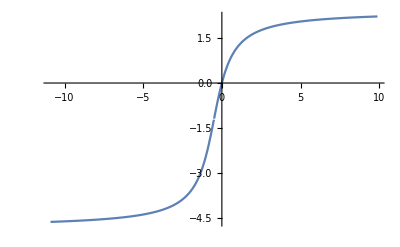

```mathematica
Plot[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),{a,-10.892304845413268,9.892304845413268}]
```

```mathematica
Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,100}]
```

-(π-6 ArcTan[67 √3])/(3 √3)

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,100}]
```

1.19925

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,1000}]
```

1.2082

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,10000}]
```

1.2091

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,100000}]
```

1.20919

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,1000000}]
```

1.2092

```mathematica
Limit[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),a->∞]
```

(4 π)/(3 √3)

```mathematica
N@Out@32
```

2.4184

```mathematica
Integrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,-100}]
```

(π-6 ArcTan[67 √3])/(3 √3)

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,-100}]
```

-1.19925

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,-1000}]
```

-1.2082

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,-10000}]
```

-1.2091

```mathematica
NIntegrate[Abs[x]/(x^2+Abs[x]+Abs[x]^3),{x,0,-1000000}]
```

-1.2092

```mathematica
Limit[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),a->-∞]
```

-(8 π)/(3 √3)

```mathematica
Limit[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),a->-∞]+Limit[-(2 (π-6 ArcTan[(1+2 a)/(√3)]))/(3 √3),a->∞]
```

-(4 π)/(3 √3)

```mathematica
Dt[f[g[x]]]
```

Dt[x] f'[g[x]] g'[x]

```mathematica
TraditionalForm[Dt[x] f'[g[x]] g'[x]]
```

ⅆx g'(x) f'(g(x))

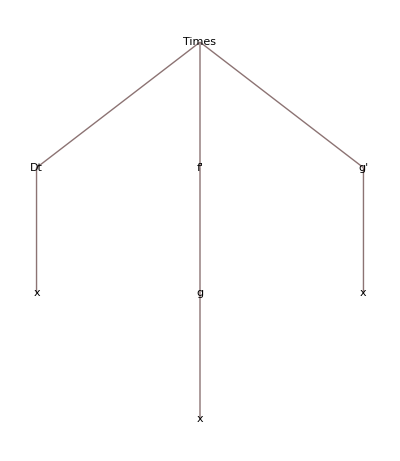

```mathematica
TreeForm@Dt[f[g[x]]]
```

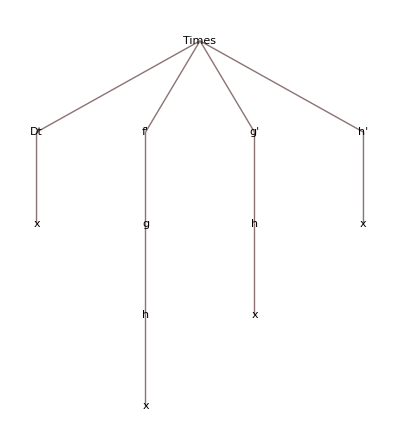

```mathematica
TreeForm@Dt[f[g[h[x]]]]
```

```mathematica
f[g[x]]==f'[g[x]]g'[x]
```

f[g[x]]==f'[g[x]] g'[x]

```mathematica
InverseFunction[f][f[g[x]]]==InverseFunction[f][f'[g[x]]g'[x]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

g[x]==f^(-1)[f'[g[x]] g'[x]]

```mathematica
x^2-x+1/2
```

1/2-x+x^2

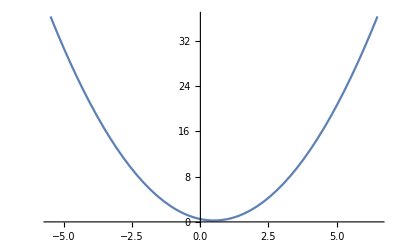

```mathematica
Plot[1/2-x+x^2,{x,-5.5,6.5}]
```

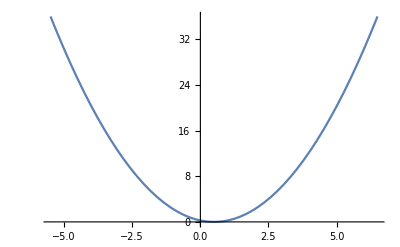

```mathematica
Plot[1/4-x+x^2,{x,-5.5,6.5}]
```

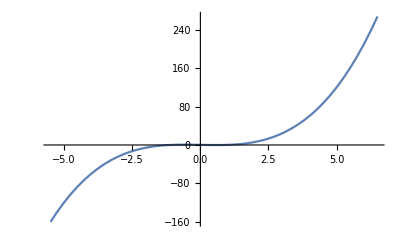

```mathematica
Plot[1/4-x+x^3,{x,-5.5,6.5}]
```

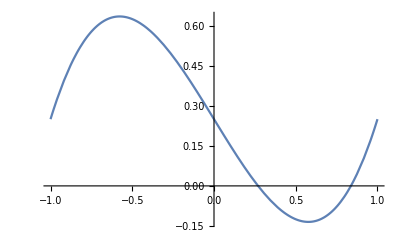

```mathematica
Plot[1/4-x+x^3,{x,-1,1}]
```

```mathematica
FullSimplify[Normalize[{x,x^3-x+1/4}].Normalize[{x,a}],{a,x}∈Reals]
```

(a-4 a x+4 x^2+4 a x^3)/(4 √((a^2+x^2) (x^2+(1/4-x+x^3)^2)))

```mathematica
Manipulate[
Plot[
(a-4 a x+4 x^2+4 a x^3)/(4 √((a^2+x^2) (x^2+(1/4-x+x^3)^2)))
,{x,-2,2},PlotRange->{-1,1}]
,{a,-1,1}]
```

```mathematica
Manipulate[
Plot[
{a,x^3-x+1/4,(a-4 a x+4 x^2+4 a x^3)/(4 √((a^2+x^2) (x^2+(1/4-x+x^3)^2)))}
,{x,-2,2},PlotRange->{-1,1}]
,{a,-1,1}]
```

```mathematica
GroebnerBasis[{x^2-2 y^2,x y-3},{x,y}]
```

{-9+2 y^4,3 x-2 y^3}

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

```mathematica
FullForm[Out[56]]
```

SeriesData[x,0,List[1,1,Rational[1,2],Rational[1,6],Rational[1,24],Rational[1,120]],0,6,1]

```mathematica
Series[Cot[x],{x,0,5}]
```

1/x-x/3-x^3/45-(2 x^5)/945+O[x]^6

```mathematica
1.33^(1/6)
```

1.04868

```mathematica
1.33^(1/12)
```

1.02405